# Three-loop on-shell vertex

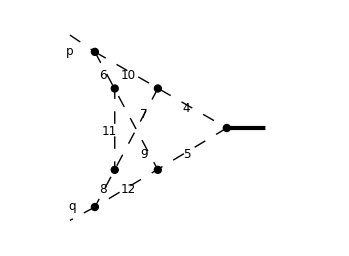

First three indices correspond to numerators.

## Finding reduction rules

#### Initialization

```mathematica
<<LiteRed`;
SetDirectory[NotebookDirectory[]];
SetDim[d];
Declare[{l,r,k,p,q},Vector];
sp[p,p]=0;sp[q,q]=0;sp[p,q]=-1/2;
```

#### Defining the basis and searching for the symmetries

```mathematica
NewBasis[v3,{r,2p·l,2 q·k,r+p,r-q,k,k-r,l,l+r,k+p,l+r-k,l+q},{r,k,l},Directory->"v3 dir"];(*Basis definition. sp[p,r] is the irreducible numerator.*)
GenerateIBP[v3]
(*IBP generation. Can be also invoked by passing GenerateIBP->True option in NewBasis call*)
AnalyzeSectors[v3,{0,0,0,__}](*Zero and simple sectors determination. Can be also invoked by passing AnalyzeSectors->True option in NewBasis call. The second argument is a pattern which claims that the sectors with sp[p,r] in the denominator should not be analyzed*)
FindSymmetries[v3](*Finding unique and mapped sectors. Can be also invoked by passing FindSymmetries->True option in NewBasis call.*)
```

#### Searching for the reduction rules

```mathematica
Timing[SolvejSector/@UniqueSectors[v3]]
```

#### Graphs

```mathematica
AttachGraph[js[v3,0,0,0,1,1,1,1,1,1,1,1,1],{
{5->7,"0"},
{6->7,"0"},
{1->3,"0"},
{4->5,"0"},
{2->4,"0"},
{3->6,"0"},
{1->5,"0"},
{3->4,"0"},
{2->6,"0"},
{0->1,"p"},
{0->2,"q"},
{7->0,"p+q"}
}];(*Attach the graph to the highest sector possible. The graphs for the subsectors are determined automatically. The external legs should start/end at vertex number 0. The internal vertices should be positive integer. The order of the internal lines should correspond to the order of denominators in the sector.*)
SetOptions[GraphPlot,MultiedgeStyle->0.3,VertexRenderingFunction->({If[#2>0,Black,Blue],Disk[#1,0.03]}&),EdgeRenderingFunction->(Replace[#3,{
"1"->{Thick,Black,Line[#1]},
"0"->{Thin,Black,Dashed,Line[#1]},
"p"->{Thickness[0.01],Blue,Line[#1]},
"q"->{Thickness[0.01],Blue,Line[#1]},
"p+q"->{Thickness[0.01],Red,Line[#1]},
_->Line[#1]
}]&)];
(*Embellish the graph output by standard Mathematica means*)
```

```mathematica
GraphPlot/@jGraph/@MIs[v3](*Draw all masters*)
```

#### Saving

```mathematica
DiskSave[v3](*Saving.*)
Quit[](*Quitting the kernel*)
```

## Applying

#### Initialization

```mathematica
<<LiteRed`;
SetDirectory[NotebookDirectory[]];
SetDim[d];
Declare[{l,r,k,p,q},Vector];
sp[p,p]=0;sp[q,q]=0;sp[p,q]=-1/2;
```

```mathematica
<<"v3 dir/v3";
```

```mathematica
Timing[IBPReduce[LoweringDRR[v3,0,0,0,1,1,1,1,1,1,1,1,1]]]
(*takes 1-1.5 hours*)
```

```mathematica
Timing[IBPReduce[RaisingDRR[v3,0,0,0,1,1,1,1,1,1,1,1,1]]]
(*takes about 1 hour*)
```